# HW3 - 2 Hopf Bifurcation -Graphics-

## a.) What is for the two systems (1) & (2), respectively? Write your answer as the vector [w_1, w_2]

-Graphics-

## b.) Determine f and g for the systems (1) and (2). Write your solution as the matrix [[f_1,g_1],[f_2,g_2]]

-Graphics-

## c.) Determine a for the two systems (1) and (2). Write you solution as the vector [a_1,a_2]. -Graphics-

```mathematica
(* Define [f1,g1] and [f2,g2] *)
f1 = -x^3;
g1 = 3*y^3;
f2 = -x^2;
g2 = 2*x^2;

(* Define w1 and w2 from the results of a) *)
w1 = 5;
w2 = -1;

(* Define the partial derivatives for system (1) *)
fxx1 = D[f1,{x,2}];
gxx1 = D[g1,{x,2}];
fyy1 = D[f1,{y,2}];
gyy1 = D[g1,{y,2}];
fxy1 = D[D[f1,{x,1}], {y,1}];
gxy1 = D[D[g1,{x,1}], {y,1}];
fxxx1 = D[f1,{x,3}];
gyyy1 = D[g1,{y,3}];
fxyy1 = D[D[f1,{x,1}], {y,2}];
gxxy1 = D[D[g1,{x,2}], {y,1}];

a1 = (fxxx1 + fxyy1 + gxxy1 + gyyy1 + (fxy1 * (fxx1 + fyy1) - gxy1 * (gxx1 + gyy1) - fxx1 * gxx1 + fyy1 * gyy1) / w1) / 16

(* Define the partial derivatives for system (2) *)
fxx2 = D[f2, {x, 2}];
gxx2 = D[g2, {x, 2}];
fyy2 = D[f2, {y, 2}];
gyy2 = D[g2, {y, 2}];
fxy2 = D[D[f2, {x, 1}], {y, 1}];
gxy2 = D[D[g2, {x, 1}], {y, 1}];
fxxx2 = D[f2, {x, 3}];
gyyy2 = D[g2, {y, 3}];
fxyy2 = D[D[f2, {x, 1}], {y, 2}];
gxxy2 = D[D[g2, {x, 2}], {y, 1}];

a2 = (fxxx2 + fxyy2 + gxxy2 + gyyy2 + (fxy2 * (fxx2 + fyy2) - gxy2 * (gxx2 + gyy2) - fxx2 * gxx2 + fyy2 * gyy2) / w2) / 16
```

3/4

-1/2

## d.) Draw phase portraits of the global dynamics for positive and negative μ for each of the systems (1) and (2). Make sure that these phase portraits verify the criteria you found in subtask c). Use a numerical solver, for example NDSolve] in Mathematica (using StreamPlot] will not give enough resolution for this task).

NDSolve::ndsz: At t == 32.0911, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 32.1867, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 32.0911, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

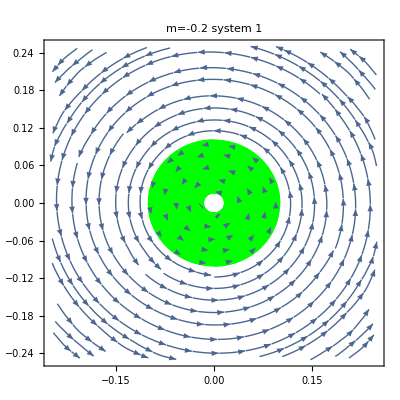

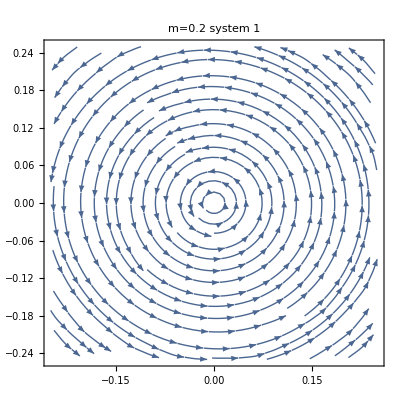

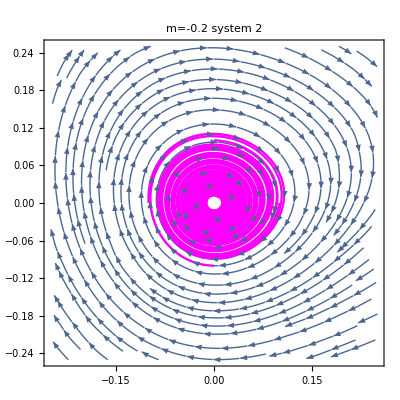

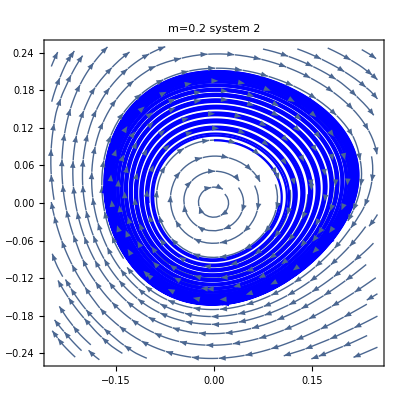

```mathematica
ClearAll["Global'*"];

m1 = 0.02;
m2 = -0.02;

(*Define system 11*)
eq11 = x'[t] == m1 * x[t] - 5 * y[t] - x[t]^3;
eq12 = y'[t] == 5 * x[t] + m1 * y[t] + 3 * y[t]^3;

(* Define system 12 *)
eq13 = x'[t] == m1 * x[t] + y[t] - x[t]^2;
eq14 = y'[t] == -x[t] + m1 * y[t] + 2 * x[t]^2;

(*Define system 21 *)
eq21 = x'[t] == m2 * x[t] - 5 * y[t] - x[t]^3;
eq22 = y'[t] == 5 * x[t] + m2 * y[t] + 3 * y[t]^3;

(* Define system 22 *)
eq23 = x'[t] == m2 * x[t] + y[t] - x[t]^2;
eq24 = y'[t] == -x[t] + m2 * y[t] + 2 * x[t]^2;

system11 = {eq11, eq12};
system12 = {eq13, eq14};

system21 = {eq21, eq22};
system22 = {eq23, eq24};

(* Define the time range for the solutions *)
t0 = 0;
tMax = 100;

(* Define initial conditions *)
FP = {0,0};
radius = 0.1;
numInitialCond = 4;
initPoints = Table[{x[0] == FP[[1]] + radius * Cos[i * 2 * Pi / numInitialCond], y[0] == FP[[2]] + radius * Sin[i * 2 * Pi / numInitialCond]}, {i,0,numInitialCond-1}];

(* Trajectories *)
sol11 = Table[NDSolve[{system11, initPoints[[i]]}, {x, y}, {t, t0, tMax}], {i, Length[initPoints]}];
sol12 = Table[NDSolve[{system12, initPoints[[i]]}, {x, y}, {t, t0, tMax}], {i, Length[initPoints]}];
sol21 = Table[NDSolve[{system21, initPoints[[i]]}, {x, y}, {t, t0, tMax}], {i, Length[initPoints]}];
sol22 = Table[NDSolve[{system22, initPoints[[i]]}, {x, y}, {t, t0, tMax}], {i, Length[initPoints]}];

(* Create parametric plots with arrows *)
parametricPlotWithArrows[sol_, style_] := 
  ParametricPlot[Evaluate[{x[t], y[t]} /. sol], {t, t0, tMax}, 
    PlotStyle -> style] /. Line[x_] :> {Arrowheads[{0., 0.04, 0.04, 0.04, 0.}], Arrow[x]};

TP11 = parametricPlotWithArrows[#, Red] & /@ sol11;
TP12 = parametricPlotWithArrows[#, Blue] & /@ sol12;
TP21 = parametricPlotWithArrows[#, Green] & /@ sol21;
TP22 = parametricPlotWithArrows[#, Magenta] & /@ sol22;

xMin = -0.5;
xMax = 0.5;
yMin = -0.5;
yMax = 0.5;

sSystem11 = {m1 * x - 5 * y - x^3,5 * x + m1 * y + 3 * y^3};
sSytsem12 = {m1 * x + y - x^2,-x + m1 * y + 2 * x^2};
sSystem21 = {m2 * x - 5 * y - x^3,5 * x + m2 * y + 3 * y^3};
sSystem22 = {m2 * x + y - x^2, -x + m2 * y + 2 * x^2};

mag = 0.5;
(* Create stream plots for each system *)
SP11 = StreamPlot[{sSystem11}, {x, xMin*mag, xMax*mag}, {y, yMin*mag, yMax*mag}, StreamColorFunction->None];
SP12 = StreamPlot[{sSytsem12}, {x, xMin*mag, xMax*mag}, {y, yMin*mag, yMax*mag}, StreamColorFunction->None];
SP21 = StreamPlot[{sSystem21}, {x, xMin*mag, xMax*mag}, {y, yMin*mag, yMax*mag}, StreamColorFunction->None];
SP22 = StreamPlot[{sSystem22}, {x, xMin*mag, xMax*mag}, {y, yMin*mag, yMax*mag}, StreamColorFunction->None];

Show[SP21, TP21, PlotLabel->"m=-0.2 system 1"]
Show[SP11, TP11, PlotLabel->"m=0.2 system 1"]
Show[SP22, TP22, PlotLabel->"m=-0.2 system 2"]
Show[SP12, TP12, PlotLabel->"m=0.2 system 2"]


Show[TP11, TP12, TP21, TP22, PlotRange -> All];
```

It can be seen, that the system 1 undergoes a subcritical bifurcation. After the bifurcation the trajectories quickly escape. 
For system 2 a supercritical behaviour is observed, the last plot approaches a limit cycle which can nicely be seen with the almost filled outer contour of the “egg” shape.